# Metastable states?

### Code and Definitions

Run this code first. Then, you may jump to any subsection.

#### Spin Operators

```mathematica
Id = {{1, 0}, {0, 1}};
Sx= (1/2){{0, 1},{1, 0}};
Sy =(1/2){{0, -I},{I, 0}};
Sz = (1/2){{1, 0},{0, -1}};
```

```mathematica
{MatrixForm[Sx], MatrixForm[Sy], MatrixForm[Sz]}
```

{(0 | 1/2
1/2 | 0),(0 | -ⅈ/2
ⅈ/2 | 0),(1/2 | 0
0 | -1/2)}

#### Local spin exchange Hamiltonian

Isotropic spin-exchange Hamiltonian for adjacent sites on a ring.

```mathematica
h = KroneckerProduct[Sx, Sx]+KroneckerProduct[Sy, Sy]+KroneckerProduct[Sz, Sz] -1/4KroneckerProduct[Id, Id];
```

```mathematica
MatrixForm[h ]
```

(0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0
0 | 1/2 | -1/2 | 0
0 | 0 | 0 | 0)

#### Probability of finding an up-spin at site x

The following function gives a list of all basis vectors that include an up-spin at site x for a chain of length L. The k-th entry equals 1 if the k-th (configuration) basis vector has an up-spin at state x. Otherwise, the entry is equal to 0. See the next section for an interpretation of the basis vectors as configuration states.

```mathematica
vec[x_, L_]:= Table[If[EvenQ[Floor[k/2^(L-x)]], 1, 0], {k, 0, 2^L-1}]
```

```mathematica
vec[1,5]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The following function gives the one-point function for the k-th eigenvector. The result is a list of length L so that each entry is {k, p(k)} with k=site and p(k)=probability of measuring an up-spin at site k. 
WARNING: E

```mathematica
Map[Function[x, Abs[x]^2], {1, 2, 3}]
```

{1,4,9}

```mathematica
t[k_,H_,keepIndices_,L_]:= Module[{Evec, norm, table, j},
Evec = Eigenvectors[H][[k]]//N;
norm = Norm[Evec]^2;
Evec= Map[Function[x, Abs[x]^2], Evec];
table =Table[{j, N[Dot[Evec, vec[j, L][[keepIndices]]]/norm]}, {j, 1, L}];
Return[table]
]
```

We rewrite the above function to have the evs=list of eigenvectors as an input so that we don’t have to compute this each time we want to compute the one-point function.

```mathematica
tp[k_, evs_,M_,L_,keepIndices_]:= Module[{Evec, norm, table, j},
Evec = evs[[k]]//N;
norm = Norm[Evec]^2;
Evec= Map[Function[x, Abs[x]^2], Evec];
table =Table[{j, N[Dot[Evec, vec[j, M][[keepIndices]]]/norm]}, {j, 1, M}];
Return[table]
]
```

#### Configurations

We translate between configuration basis and tensor basis, e.g.
{|↑↑⟩,|↑↓⟩, |↓↑⟩, |↓↓⟩} ->{(1
0) ⊗(1
0) , (1
0) ⊗(0
1), (0
1) ⊗(1
0) , (0
1) ⊗(0
1)} ->{(1
0
0
0) , (0
1
0
0)  , (0
0
1
0)   , (0
0
0
1) } 
Let L be the length of the line segment. Denote the basis vectors on the right by e_k, k =1, ..., 2^L, of length/dimension 2^L so that all the entries are zero except for the k-th entry which is 1. The example above is for L=2. We can translate to the configuration basis on the left, i.e. the basis determined by the location of the up-arrows, by writing 2^L-k in base 2. See example below for L=5. The 1-digits represent up-arrows and the 0-digits represent down-arrow. Note that you should think of each number to be made up of L {0,1}-digits by padding 0’s to the left if necessary.

```mathematica
L=5;
Table[BaseForm[2^L-k, 2], {k ,1, 2^L}]
```

{11111_2,11110_2,11101_2,11100_2,11011_2,11010_2,11001_2,11000_2,10111_2,10110_2,10101_2,10100_2,10011_2,10010_2,10001_2,10000_2,1111_2,1110_2,1101_2,1100_2,1011_2,1010_2,1001_2,1000_2,111_2,110_2,101_2,100_2,11_2,10_2,1_2,0_2}

### Hamiltonian for a line segment

#### L=3

Let consider one line segment with L = 3 sites.
    H = Hamiltonian for one line segment of length L.
    hRing = spin exchange operator for the first and last site to make the segment into a ring.
We plot the eigenvalues.

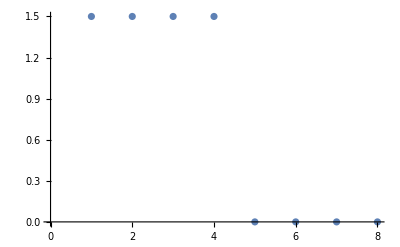

```mathematica
L=3;
hRing = KroneckerProduct[Sx, IdentityMatrix[2^(L-2)], Sx] + KroneckerProduct[Sy, IdentityMatrix[2^(L-2)], Sy]+KroneckerProduct[Sz, IdentityMatrix[2^(L-2)], Sz]-(1/4) IdentityMatrix[2^L];
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-1-k)]], {k, 1, L-1}] + hRing ;
ListPlot[Eigenvalues[-H]]
```

#### Hamiltonian for the ring of length L and fixed number of down spins

Here we trim the Hamiltonian for the ring only to consider states which contain the specified number of down spins.
For example, with a ring of length L=3, we can consider states which have exactly two down spins. We also return the kept indices which keep track of the rows and columns of the original hamiltonian we kept. These will then be used to modify the output of the vec function so that we can properly compute the one-point probabilities.

```mathematica
HringNdownspins[L_,NumDownspins_] := Module[{hRing, H,basis,keepIndices,trimmedH, removeIndices},
hRing = KroneckerProduct[Sx, IdentityMatrix[2^(L-2)], Sx] + KroneckerProduct[Sy, IdentityMatrix[2^(L-2)], Sy]+KroneckerProduct[Sz, IdentityMatrix[2^(L-2)], Sz]-(1/4) IdentityMatrix[2^L];
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] + hRing;
basis = Table[IntegerDigits[2^L-k, 2,L], {k ,1, 2^L}];
keepIndices = Flatten[Position[basis,x_/;Count[x,0]==NumDownspins]];
(*Sanity check if you want to make sure you're keeping the right indices:
For a single layer, L=3, N=2, indices should be 4, 6, and 7 
Print[keepIndices]; *)
trimmedH = H[[keepIndices,keepIndices]];
{trimmedH, keepIndices}
]
```

```mathematica
{H3L2N, keepIndices} = HringNdownspins[3,2];
MatrixForm[H3L2N]
keepIndices
```

(-1 | 1/2 | 1/2
1/2 | -1 | 1/2
1/2 | 1/2 | -1)

{4,6,7}

HringNdownspins[3,2,True,1,6]

(-1 | 1/2 | 1/2
1/2 | -1 | 1/2
1/2 | 1/2 | -1)

{4,6,7}

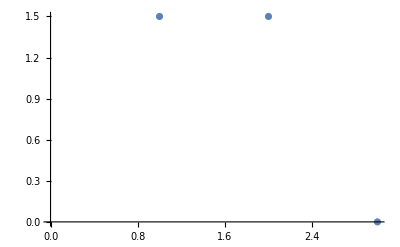

{{-1,0,1},{-1,1,0},{1,1,1}}

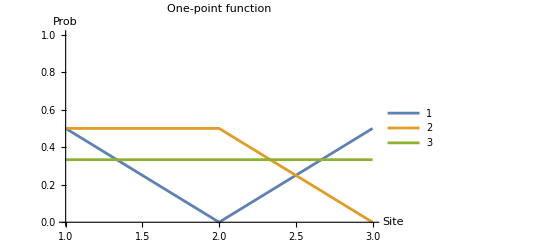

```mathematica
ListPlot[Eigenvalues[-H3L2N]]
Evecs = Eigenvectors[-H3L2N]
T=Table[t[k, H3L2N,keepIndices,3], {k, 1, 3}];
ListPlot[{T[[1]], T[[2]], T[[3]]}, Joined->True, PlotRange->{{1, 3}, {0,1}}, PlotLabel-> "One-point function", AxesLabel->{"Site", "Prob"},PlotLegends->Automatic]
```

```mathematica
{H11L4N, keepIndices2} = HringNdownspins[11,4];
MatrixForm[H11L4N]
keepIndices2
```

{16,24,28,30,31,40,44,46,47,52,54,55,58,59,61,72,76,78,79,84,86,87,90,91,93,100,102,103,106,107,109,114,115,117,121,136,140,142,143,148,150,151,154,155,157,164,166,167,170,171,173,178,179,181,185,196,198,199,202,203,205,210,211,213,217,226,227,229,233,241,264,268,270,271,276,278,279,282,283,285,292,294,295,298,299,301,306,307,309,313,324,326,327,330,331,333,338,339,341,345,354,355,357,361,369,388,390,391,394,395,397,402,403,405,409,418,419,421,425,433,450,451,453,457,465,481,520,524,526,527,532,534,535,538,539,541,548,550,551,554,555,557,562,563,565,569,580,582,583,586,587,589,594,595,597,601,610,611,613,617,625,644,646,647,650,651,653,658,659,661,665,674,675,677,681,689,706,707,709,713,721,737,772,774,775,778,779,781,786,787,789,793,802,803,805,809,817,834,835,837,841,849,865,898,899,901,905,913,929,961,1032,1036,1038,1039,1044,1046,1047,1050,1051,1053,1060,1062,1063,1066,1067,1069,1074,1075,1077,1081,1092,1094,1095,1098,1099,1101,1106,1107,1109,1113,1122,1123,1125,1129,1137,1156,1158,1159,1162,1163,1165,1170,1171,1173,1177,1186,1187,1189,1193,1201,1218,1219,1221,1225,1233,1249,1284,1286,1287,1290,1291,1293,1298,1299,1301,1305,1314,1315,1317,1321,1329,1346,1347,1349,1353,1361,1377,1410,1411,1413,1417,1425,1441,1473,1540,1542,1543,1546,1547,1549,1554,1555,1557,1561,1570,1571,1573,1577,1585,1602,1603,1605,1609,1617,1633,1666,1667,1669,1673,1681,1697,1729,1794,1795,1797,1801,1809,1825,1857,1921}

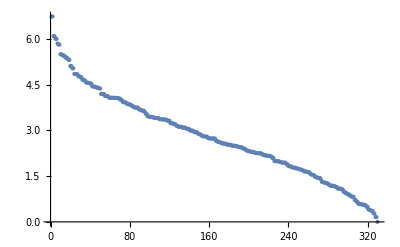

$Aborted

$Aborted

Part::partd: Part specification T2⟦1⟧ is longer than depth of object.

Part::partd: Part specification T2⟦2⟧ is longer than depth of object.

Part::partd: Part specification T2⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

(-1 | 1/2 | 1/2
1/2 | -1 | 1/2
1/2 | 1/2 | -1)

-Graphics-

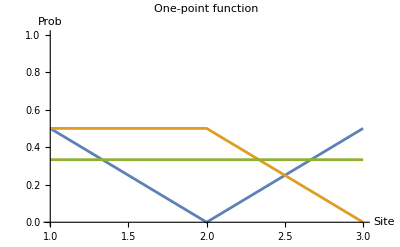

```mathematica
ListPlot[Eigenvalues[-H11L4N]]
Evecs = Eigenvectors[-H11L4N];
T2=Table[t[k, H11L4N,keepIndices2,11], {k, 1, 2^11}]
ListPlot[{T2[[1]], T2[[2]], T2[[3]]}, Joined->True, PlotRange->{{1, 11}, {0,1}}, PlotLabel-> "One-point function", AxesLabel->{"Site", "Prob"}]
```

Table of one-point functions for all eigenstates.

```mathematica
T = Table[t[k], {k, 1, 2^L}];
```

We plot the one-point functions below. We plot states with same eigenvalues together

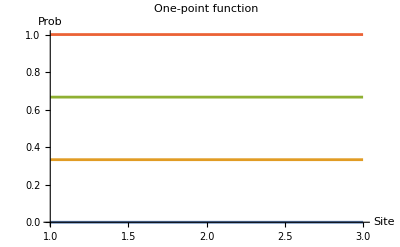

```mathematica
ListPlot[{T[[5]], T[[6]], T[[7]], T[[8]]}, Joined->True, PlotRange->{{1, L}, {0,1}}, PlotLabel-> "One-point function", AxesLabel->{"Site", "Prob"}]
```

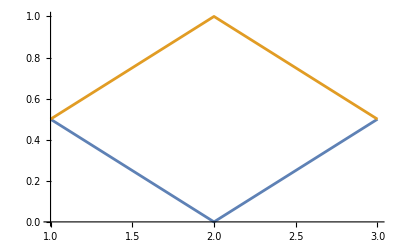

```mathematica
ListPlot[{T[[3]], T[[4]]}, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

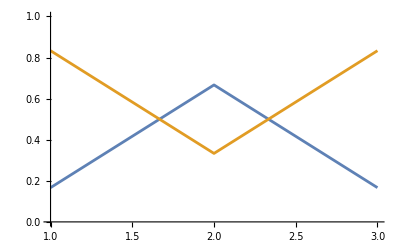

```mathematica
ListPlot[{T[[1]], T[[2]]}, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

#### L= 5

```mathematica
L=5;
```

H  = Hamiltonian

```mathematica
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-1-k)]], {k, 1, L-1}];
```

Eigenvalues

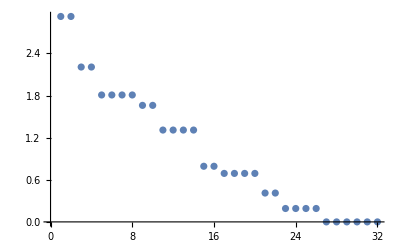

```mathematica
ListPlot[Eigenvalues[-H]]
```

Table of one-point functions

```mathematica
T = Table[t[k], {k, 1, 2^L}];
```

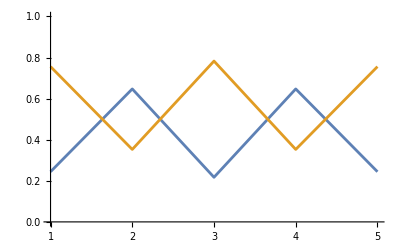

```mathematica
ListPlot[{T[[1]], T[[2]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

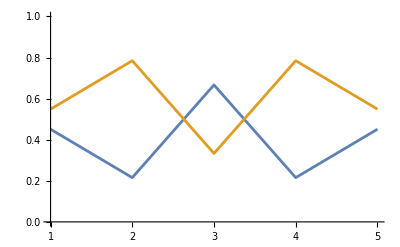

```mathematica
ListPlot[{T[[3]], T[[4]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

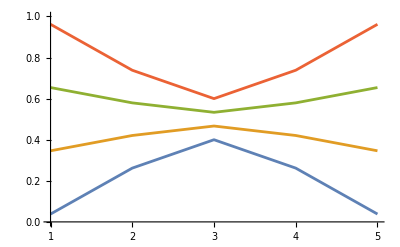

```mathematica
ListPlot[{T[[5]], T[[6]], T[[7]], T[[8]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

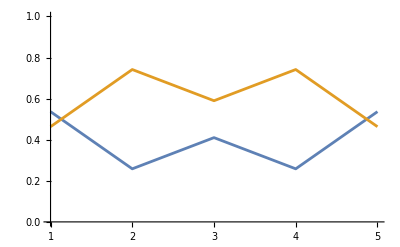

```mathematica
ListPlot[{T[[9]], T[[10]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

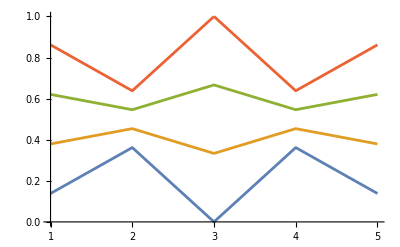

```mathematica
ListPlot[{T[[11]], T[[12]], T[[13]], T[[14]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

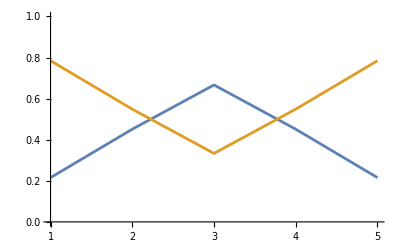

```mathematica
ListPlot[{T[[15]], T[[16]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

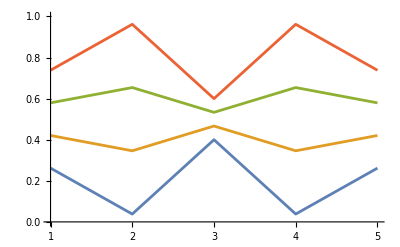

```mathematica
ListPlot[{T[[17]], T[[18]], T[[19]], T[[20]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

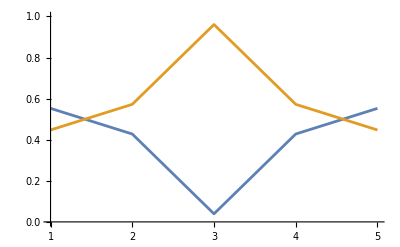

```mathematica
ListPlot[{T[[21]], T[[22]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

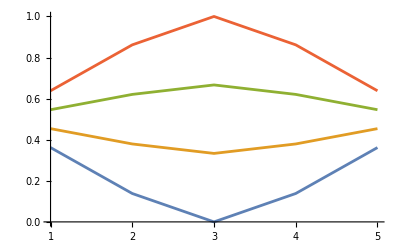

```mathematica
ListPlot[{T[[23]], T[[24]], T[[25]], T[[26]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

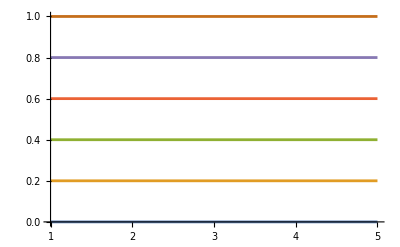

```mathematica
ListPlot[{T[[27]], T[[28]], T[[29]], T[[30]], T[[31]], T[[32]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

### Parallel lines

Let’s do two parallel lines. 
    M= total number of sites. 
    L= sites per layer = M/2.
    H1 = Hamiltonian for first layer.
    H2 = Hamiltonian for second layer.
    H12 = Hamiltonian between layers.
    Hp = Hamiltonian for parallel layers
    InterLayerCoupling = coupling strength between lines

```mathematica
ParallelLines[M_,L_,InterLayerCoupling_]:=Module[{H1,H2,H12,basis,keepIndices,Hp,trimmedHp},
H1 =  Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}];
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}]+ Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M];
Hp = -H1 - H2 + (InterLayerCoupling*H12);

basis = Table[IntegerDigits[2^M-k, 2,M], {k ,1, 2^M}];
(* We consider the case where half the spins are flipped. I.e. ferromagnetic within the layer, antiferromagnetic between layers. Ultimately, we want to evolve the state where one spin in each layer is flipped *)
keepIndices = Flatten[Position[basis,x_/;Count[x,0]==L]];
trimmedHp = Hp[[keepIndices,keepIndices]];
Return[{trimmedHp, keepIndices}]
]
```

```mathematica
{Hp, keepIndices} = ParallelLines[8,4,1/10];
MatrixForm[Hp]
keepIndices

(*ListPlot[Eigenvalues[H]]*)
```

(-1/5 | 0 | 0 | 0 | 1/20 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9/10 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 7/5 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 7/5 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/20 | 0 | 0 | -1/2 | 4/5 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 0 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | -1/2 | 19/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/20 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 9/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 7/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 19/10 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 19/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 4/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 9/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 19/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19/10 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 3 | -1/2 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 12/5 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 12/5 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 14/5 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 19/10 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 12/5 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 9/5 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | -1/2 | 12/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 4/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20
1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/5 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 9/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 12/5 | -1/2 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 9/5 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 2 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 12/5 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 19/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 14/5 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 12/5 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 12/5 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | -1/2 | 3 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 19/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 19/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 9/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/5 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 19/10 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 7/5 | -1/2 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 19/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/5 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 9/5 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 1/20
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 19/10 | -1/2 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 7/5 | 0 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 4/5 | -1/2 | 0 | 0 | 1/20
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 7/5 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 7/5 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 9/10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | 0 | 1/20 | 0 | 0 | 0 | -1/5)

{16,24,28,30,31,40,44,46,47,52,54,55,58,59,61,72,76,78,79,84,86,87,90,91,93,100,102,103,106,107,109,114,115,117,121,136,140,142,143,148,150,151,154,155,157,164,166,167,170,171,173,178,179,181,185,196,198,199,202,203,205,210,211,213,217,226,227,229,233,241}

```mathematica
Eigs = Eigenvalues[Hp];
```

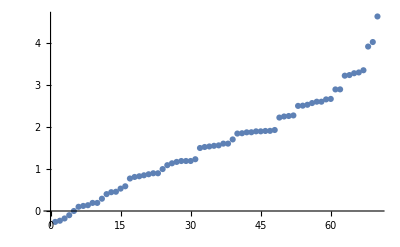

```mathematica
ListPlot[Sort[Eigs, Less]]
```

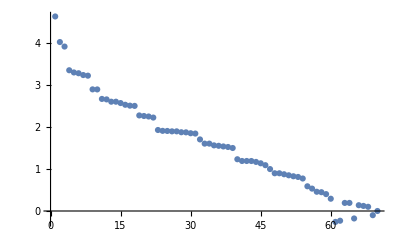

```mathematica
ListPlot[Eigs]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
Length[Hp]
```

```mathematica
OnePoint = Table[tp[k, EVs,8,4,keepIndices], {k, 1, Length[Hp]}];
```

```mathematica
Length[OnePoint]
```

70

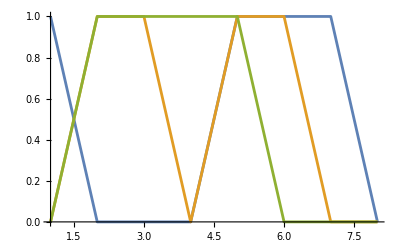

```mathematica
ListPlot[{OnePoint[[32]],OnePoint[[33]],OnePoint[[34]]}, Joined->True, PlotRange->{{1, 8}, {0,1}}]
```

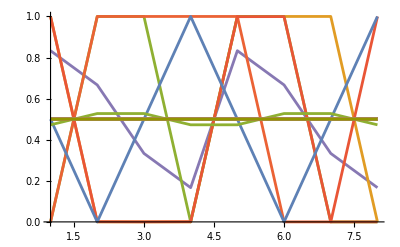

```mathematica
ListPlot[OnePoint,Joined->True,PlotRange->{{1,8},{0,1}}]
```

```mathematica
ListPlot[OnePoint[[46]],]
```

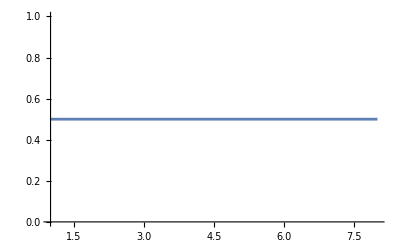

## Dynamics for specific initial conditions

Here we create the wave function
 
for a specific initial configuration where  corresponds to the coefficient of the k’th eigenvector in the configuration’s expansion in terms of the eigenbasis , and   is the corresponding eigenvalue.

```mathematica
WaveFunction[Eigenvalues_,Eigenvectors_,ConfigurationIndex_,t_,hbar_]:=Sum[Eigenvectors[[k]][[ConfigurationIndex]]*Exp[-ⅈ*Eigenvalues[[k]]*t/hbar]*Eigenvectors[[k]],{k,1,Length[Eigenvectors]}]
```

```mathematica
Length[EVs[[1]]]
```

70

```mathematica
keepIndices
```

{16,24,28,30,31,40,44,46,47,52,54,55,58,59,61,72,76,78,79,84,86,87,90,91,93,100,102,103,106,107,109,114,115,117,121,136,140,142,143,148,150,151,154,155,157,164,166,167,170,171,173,178,179,181,185,196,198,199,202,203,205,210,211,213,217,226,227,229,233,241}

```mathematica
EVs[[1]].EVs[[2]]//N
```

2.72848×10^-12

```mathematica
Table[EVs[[i]].EVs[[j]]//N,{i,1,10},{j,1,10}]//MatrixForm//Chop
A= Map[Function[x, Norm[x]^2], EVs]//N
```

(3.54439×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16999.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.77624×10^8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 28912.6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 15075.8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11808.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 16648.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 78388.6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 358529. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.)

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -58928262284248284264642595791593037423512550380890922283702819856790846641494090582325128594841735510966142714236809211181584037471162244264016847269212857219024891208813984737411480227667439310278650128301329978674785717476829243426165506802413451774081391840022820222675690593818047241175338808239427503177903617090«1»416685738647314327375145«268»0827162254075833129078921«1»«1».

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -10883992957680733684538664317344942922819220235302334578965179125707312580648535049071991322724056482263317330619010775615497641245147443268488693341035514908736613314978759273688189598924129608568058132858995971279899176461118882755912003681415492133494051320911496481621499851653823003926642398473800132931811165037«1»769614522676267476324396«267»4607172113485725329478471«1»«1».

General::stop: Further output of N::meprec will be suppressed during this calculation.

{3.54439×10^6,16999.2,1.77624×10^8,28912.6,15075.8,11808.2,16648.1,78388.6,358529.,24.,85.3945,231.032,54.6274,54.6274,148.05,273.223,184.279,163.882,299145.,4.44681×10^21,475.769,28500.,25363.8,16.4307,19524.8,16.,8.,73536.5,3714.77,21012.5,7097.54,2.6734×10^151,4.54233×10^210,1.81684×10^211,16.0558,688.308,88.0541,24.5396,2.50898×10^6,115.399,8.46401×10^68,9.37258,9.89552,2.16592×10^6,22.5834,1.48033×10^35,40.,40.,16.,196.228,112767.,26.5823,67790.4,3388.28,3009.63,24.,2066.78,357.895,483.025,23.4315,5.05874,2.52009,145.941,273.137,3.51172,124.125,15.8243,236.721,10.,70.}

```mathematica
EVs[[2]]//N//MatrixForm
```

(0.
-1.
0.886855
-1.08331
0.
0.886855
-0.632507
0.
1.08331
7.40333
-22.4339
9.74739
9.74739
-4.6054
0.
-1.08331
0.
0.632507
-0.886855
-22.4339
68.4814
-24.0594
-24.0594
0.
4.6054
9.74739
-24.0594
0.
0.
24.0594
-9.74739
-1.
0.886855
-1.08331
0.
0.
1.08331
-0.886855
1.
9.74739
-24.0594
0.
0.
24.0594
-9.74739
-4.6054
0.
24.0594
24.0594
-68.4814
22.4339
0.886855
-0.632507
0.
1.08331
0.
4.6054
-9.74739
-9.74739
22.4339
-7.40333
-1.08331
0.
0.632507
-0.886855
0.
1.08331
-0.886855
1.
0.)

```mathematica
Sum[EVs[[k]][[1]]*EVs[[k]]/A[[k]],{k,1,Length[EVs]}]//N//Chop
```

General::munfl: -1.5342×10^-292 8.62636×10^-32 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.80518×10^-292 8.62636×10^-32 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.5342×10^-292 8.62636×10^-32 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
WaveFunction[Eigs,EVs,46,0,1]//N
```

{-105.669,14434.5,-6477.81,9887.15,274198.,-1594.93,2338.16,-336598.,9877.04,-92414.,-1.22466×10^6,2.618×10^6,2.618×10^6,-2.39476×10^202,1.74106×10^6,-14362.3,345005.,2356.65,-6476.07,1.34126×10^6,-100743.,-6.07968×10^6,-3.07592×10^202,-2.18752×10^190,-5.63194×10^6,-2.57796×10^6,3.07592×10^202,-66330.,-73784.8,-6.07993×10^6,2.11684×10^167,14439.3,-6474.4,-1.6643×10^180,274198.,8.89664×10^204,-14372.4,-1593.2,14434.,-2.57796×10^6,3.07592×10^202,-73784.8,-66330.,-6.07993×10^6,3.71171×10^171,4.35667×10^198,-1.61362×10^7,6.16221×10^6,6.16221×10^6,-100156.,-1.22482×10^6,-1591.52,2340.16,-1.007×10^171,9875.63,-1.91096×10^6,5.77784×10^6,-2.11684×10^167,-2.57785×10^6,1.3411×10^6,-92350.4,-14360.9,-5.29643×10^137,2354.65,-1.12558×10^105,-290420.,-8.67173×10^98,2.08726×10^99,14429.2,-105.669}

```mathematica
Evaluation = Table[WaveFunction[Eigs,EVs,46,t,1],{t,0,1,0.2}]
OnePtWave = Table[tp[k, Evaluation,8,4,keepIndices], {k, 1, Length[Evaluation]}]
```

General::munfl: 8.62636×10^-32 (3.06673×10^-280+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.62636×10^-32 (-5.60729×10^-280+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.62636×10^-32 (3.06673×10^-280+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-105.669+0. ⅈ,14436.5+0. ⅈ,-6471.27+0. ⅈ,9900.1+0. ⅈ,274216.+0. ⅈ,-1598.64+0. ⅈ,2338.99+0. ⅈ,-336590.+0. ⅈ,9888.82+0. ⅈ,-92414.6+0. ⅈ,-1.22465×10^6+0. ⅈ,2.61801×10^6+0. ⅈ,2.61801×10^6+0. ⅈ,-5.6318×10^6+0. ⅈ,1.74109×10^6+0. ⅈ,-14374.1+0. ⅈ,344998.+0. ⅈ,2355.82+0. ⅈ,-6472.36+0. ⅈ,1.34125×10^6+0. ⅈ,-100743.+0. ⅈ,-6.07967×10^6+0. ⅈ,-6.07967×10^6+0. ⅈ,1.59554×10^7+0. ⅈ,-5.63192×10^6+0. ⅈ,-2.57798×10^6+0. ⅈ,6.16246×10^6+0. ⅈ,-66330.+0. ⅈ,-73784.8+0. ⅈ,-6.07993×10^6+0. ⅈ,2.11684×10^167+0. ⅈ,14436.5+0. ⅈ,-6471.27+0. ⅈ,9900.1+0. ⅈ,274216.+0. ⅈ,-290438.+0. ⅈ,-14385.3+0. ⅈ,-1599.73+0. ⅈ,14432.+0. ⅈ,-2.57798×10^6+0. ⅈ,6.16246×10^6+0. ⅈ,-73784.8+0. ⅈ,-66330.+0. ⅈ,-6.07993×10^6+0. ⅈ,3.71169×10^171+0. ⅈ,5.77796×10^6+0. ⅈ,-1.61362×10^7+0. ⅈ,6.1622×10^6+0. ⅈ,6.1622×10^6+0. ⅈ,-100156.+0. ⅈ,-1.22481×10^6+0. ⅈ,-1598.64+0. ⅈ,2338.99+0. ⅈ,-1.007×10^171+0. ⅈ,9888.82+0. ⅈ,-1.91099×10^6+0. ⅈ,5.77782×10^6+0. ⅈ,-2.11684×10^167+0. ⅈ,-2.57787×10^6+0. ⅈ,1.34109×10^6+0. ⅈ,-92349.9+0. ⅈ,-14374.1+0. ⅈ,-5.29643×10^137+0. ⅈ,2354.65+0. ⅈ,-1.12558×10^105+0. ⅈ,-290438.+0. ⅈ,-8.67173×10^98+0. ⅈ,2.08726×10^99+0. ⅈ,14429.2+0. ⅈ,-105.669+0. ⅈ},{-67.612+59.1807 ⅈ,13469.2-4367.92 ⅈ,-5003.09+3665.88 ⅈ,5486.49-9191.35 ⅈ,192773.-196412. ⅈ,-1536.17+248.274 ⅈ,1256.98-1948.78 ⅈ,-235862.+241250. ⅈ,5478.23-9183.96 ⅈ,-85886.1+28778.2 ⅈ,-862836.+872936. ⅈ,1.86621×10^6-1.8263×10^6 ⅈ,1.86621×10^6-1.8263×10^6 ⅈ,-3.97875×10^6+3.99201×10^6 ⅈ,1.21393×10^6-1.26261×10^6 ⅈ,-11729.3+7903.58 ⅈ,246576.-240205. ⅈ,1273.88-1952.97 ⅈ,-5005.57+3664.62 ⅈ,952423.-940851. ⅈ,-62987.8+76699.1 ⅈ,-4.31422×10^6+4.28168×10^6 ⅈ,-4.31422×10^6+4.28168×10^6 ⅈ,1.13008×10^7-1.12646×10^7 ⅈ,-3.97885×10^6+3.99208×10^6 ⅈ,-1.81097×10^6+1.84484×10^6 ⅈ,4.34946×10^6-4.36788×10^6 ⅈ,-48921.3+37380.6 ⅈ,-57091.8+37803.2 ⅈ,-4.31441×10^6+4.28185×10^6 ⅈ,2.00843×10^167-6.68742×10^166 ⅈ,13469.2-4367.92 ⅈ,-5003.09+3665.88 ⅈ,5486.49-9191.35 ⅈ,192773.-196412. ⅈ,-206879.+202462. ⅈ,-11737.6+7910.97 ⅈ,-1538.65+247.008 ⅈ,13466.5-4364.75 ⅈ,-1.81097×10^6+1.84484×10^6 ⅈ,4.34946×10^6-4.36788×10^6 ⅈ,-57091.8+37803.2 ⅈ,-48921.3+37380.6 ⅈ,-4.31441×10^6+4.28185×10^6 ⅈ,3.52158×10^171-1.17276×10^171 ⅈ,4.09738×10^6-4.06729×10^6 ⅈ,-1.14122×10^7+1.14065×10^7 ⅈ,4.34927×10^6-4.36771×10^6 ⅈ,4.34927×10^6-4.36771×10^6 ⅈ,-62589.9+76263.9 ⅈ,-862934.+873066. ⅈ,-1536.17+248.274 ⅈ,1256.98-1948.78 ⅈ,-9.55429×10^170+3.18127×10^170 ⅈ,5478.23-9183.96 ⅈ,-1.37144×10^6+1.31658×10^6 ⅈ,4.09726×10^6-4.06722×10^6 ⅈ,-2.00843×10^167+6.68742×10^166 ⅈ,-1.81089×10^6+1.84476×10^6 ⅈ,952321.-940719. ⅈ,-85839.6+28738.6 ⅈ,-11729.3+7903.58 ⅈ,-5.02518×10^137+1.67322×10^137 ⅈ,1272.71-1952.92 ⅈ,-1.06793×10^105+3.55587×10^104 ⅈ,-206879.+202462. ⅈ,-8.22763×10^98+2.73953×10^98 ⅈ,1.98037×10^99-6.59399×10^98 ⅈ,13463.7-4364.63 ⅈ,-67.612+59.1807 ⅈ},{5.56125+46.9891 ⅈ,11000.1-7667.46 ⅈ,-1564.68+5198. ⅈ,-4733.12-11681.3 ⅈ,-4136.38-277843. ⅈ,-1497.06+343.539 ⅈ,-1030.89-2070.07 ⅈ,6804.32+339490. ⅈ,-4734.2-11670.8 ⅈ,-69143.7+50350.3 ⅈ,12112.7+1.23495×10^6 ⅈ,48629.6-2.59221×10^6 ⅈ,48629.6-2.59221×10^6 ⅈ,14787.9+5.64822×10^6 ⅈ,-58520.9-1.77854×10^6 ⅈ,-4893.08+12544.6 ⅈ,8187.47-342047. ⅈ,-1014.56-2079.66 ⅈ,-1570.02+5198.09 ⅈ,14342.-1.3318×10^6 ⅈ,20243.9+93216. ⅈ,-43723.+6.07445×10^6 ⅈ,-43723.+6.07445×10^6 ⅈ,50960.3-1.59586×10^7 ⅈ,14734.1+5.64832×10^6 ⅈ,40045.7+2.60404×10^6 ⅈ,-23633.8-6.16836×10^6 ⅈ,-11272.3+46592.5 ⅈ,-20721.4+48963.8 ⅈ,-43736.7+6.07469×10^6 ⅈ,1.69431×10^167-1.26899×10^167 ⅈ,11000.1-7667.46 ⅈ,-1564.68+5198. ⅈ,-4733.12-11681.3 ⅈ,-4136.38-277843. ⅈ,-5223.85+286773. ⅈ,-4894.16+12555. ⅈ,-1502.4+343.632 ⅈ,11001.5-7664.28 ⅈ,40045.7+2.60404×10^6 ⅈ,-23633.8-6.16836×10^6 ⅈ,-20721.4+48963.8 ⅈ,-11272.3+46592.5 ⅈ,-43736.7+6.07469×10^6 ⅈ,2.97105×10^171-2.22522×10^171 ⅈ,38391.4-5.76043×10^6 ⅈ,-8251.09+1.61325×10^7 ⅈ,-23650.5-6.16811×10^6 ⅈ,-23650.5-6.16811×10^6 ⅈ,20192.7+92621.1 ⅈ,12154.8+1.23512×10^6 ⅈ,-1497.06+343.539 ⅈ,-1030.89-2070.07 ⅈ,-8.05998×10^170+6.0367×10^170 ⅈ,-4734.2-11670.8 ⅈ,-67152.4+1.87283×10^6 ⅈ,38329.2-5.76032×10^6 ⅈ,-1.69431×10^167+1.26899×10^167 ⅈ,40046.7+2.60393×10^6 ⅈ,14381.5-1.33163×10^6 ⅈ,-69139.3+50298.8 ⅈ,-4893.08+12544.6 ⅈ,-4.23923×10^137+3.17506×10^137 ⅈ,-1015.72-2079.56 ⅈ,-9.00905×10^104+6.74752×10^104 ⅈ,-5223.85+286773. ⅈ,-6.94081×10^98+5.19847×10^98 ⅈ,1.67064×10^99-1.25126×10^99 ⅈ,10998.7-7664.05 ⅈ,5.56125+46.9891 ⅈ},{27.3746-38.3229 ⅈ,8023.25-9472.17 ⅈ,1626.09+3925.62 ⅈ,-13729.2-5284.41 ⅈ,-201775.-196144. ⅈ,-1723.02+441.353 ⅈ,-2446.68-102.502 ⅈ,248021.+236152. ⅈ,-13723.4-5276.78 ⅈ,-48796.5+61639. ⅈ,890315.+871454. ⅈ,-1.77615×10^6-1.85503×10^6 ⅈ,-1.77615×10^6-1.85503×10^6 ⅈ,4.01516×10^6+3.99622×10^6 ⅈ,-1.32959×10^6-1.23767×10^6 ⅈ,3212.67+11962.9 ⅈ,-232400.-247179. ⅈ,-2433.38-118.567 ⅈ,1619.46+3930.29 ⅈ,-922724.-946808. ⅈ,82849.7+37388.7 ⅈ,4.24934×10^6+4.33482×10^6 ⅈ,4.24934×10^6+4.33482×10^6 ⅈ,-1.12335×10^7-1.13407×10^7 ⅈ,4.01517×10^6+3.99633×10^6 ⅈ,1.88918×10^6+1.82867×10^6 ⅈ,-4.38666×10^6-4.34419×10^6 ⅈ,15008.7+23245.7 ⅈ,5562.57+29159.6 ⅈ,4.2495×10^6+4.335×10^6 ⅈ,1.20664×10^167-1.73926×10^167 ⅈ,8023.25-9472.17 ⅈ,1626.09+3925.62 ⅈ,-13729.2-5284.41 ⅈ,-201775.-196144. ⅈ,196305.+204211. ⅈ,3218.55+11970.5 ⅈ,-1729.65+446.023 ⅈ,8027.35-9473.01 ⅈ,1.88918×10^6+1.82867×10^6 ⅈ,-4.38666×10^6-4.34419×10^6 ⅈ,5562.57+29159.6 ⅈ,15008.7+23245.7 ⅈ,4.2495×10^6+4.335×10^6 ⅈ,2.11578×10^171-3.04983×10^171 ⅈ,-4.02636×10^6-4.09473×10^6 ⅈ,1.13952×10^7+1.14133×10^7 ⅈ,-4.38651×10^6-4.34401×10^6 ⅈ,-4.38651×10^6-4.34401×10^6 ⅈ,82371.+37013.8 ⅈ,890487.+871547. ⅈ,-1723.02+441.353 ⅈ,-2446.68-102.502 ⅈ,-5.74012×10^170+8.27381×10^170 ⅈ,-13723.4-5276.78 ⅈ,1.24277×10^6+1.35262×10^6 ⅈ,-4.02636×10^6-4.09461×10^6 ⅈ,-1.20664×10^167+1.73926×10^167 ⅈ,1.8891×10^6+1.82858×10^6 ⅈ,-922553.-946713. ⅈ,-48829.1+61612.8 ⅈ,3212.67+11962.9 ⅈ,-3.01908×10^137+4.3517×10^137 ⅈ,-2434.54-118.421 ⅈ,-6.41603×10^104+9.24806×10^104 ⅈ,196305.+204211. ⅈ,-4.94307×10^98+7.12495×10^98 ⅈ,1.18979×10^99-1.71496×10^99 ⅈ,8024.55-9472.66 ⅈ,27.3746-38.3229 ⅈ},{-54.9242-118.918 ⅈ,5412.55-10161.2 ⅈ,2648.4+1060.45 ⅈ,-15180.1+6201.78 ⅈ,-284731.+1922.3 ⅈ,-2153.3+944.946 ⅈ,-1536.69+2367.23 ⅈ,345197.-8369.98 ⅈ,-15171.7+6202.69 ⅈ,-30907.9+64851.7 ⅈ,1.25762×10^6-10254.6 ⅈ,-2.54527×10^6-48201.1 ⅈ,-2.54527×10^6-48201.1 ⅈ,5.68221×10^6-4309.68 ⅈ,-1.85104×10^6+51721.4 ⅈ,8939.42+6452.75 ⅈ,-336197.-11079.4 ⅈ,-1530.2+2345.53 ⅈ,2644.67+1070.77 ⅈ,-1.31129×10^6-15785.8 ⅈ,75458.5-45304.7 ⅈ,6.06673×10^6+72578.5 ⅈ,6.06673×10^6+72578.5 ⅈ,-1.59676×10^7-99816.9 ⅈ,5.68226×10^6-4234.64 ⅈ,2.65165×10^6-30690.3 ⅈ,-6.17778×10^6+31531.8 ⅈ,7770.72-9072.72 ⅈ,780.853+370.203 ⅈ,6.06695×10^6+72593.2 ⅈ,5.95391×10^166-2.03138×10^167 ⅈ,5412.55-10161.2 ⅈ,2648.4+1060.45 ⅈ,-15180.1+6201.78 ⅈ,-284731.+1922.3 ⅈ,279814.+4035.92 ⅈ,8947.84+6453.65 ⅈ,-2157.02+955.273 ⅈ,5414.84-10167.7 ⅈ,2.65165×10^6-30690.3 ⅈ,-6.17778×10^6+31531.8 ⅈ,780.853+370.203 ⅈ,7770.72-9072.72 ⅈ,6.06695×10^6+72593.2 ⅈ,1.04397×10^171-3.56168×10^171 ⅈ,-5.72361×10^6-50132. ⅈ,1.6122×10^7+17968.1 ⅈ,-6.17756×10^6+31550. ⅈ,-6.17756×10^6+31550. ⅈ,74844.3-45212.5 ⅈ,1.25783×10^6-10317.6 ⅈ,-2153.3+944.946 ⅈ,-1536.69+2367.23 ⅈ,-2.83233×10^170+9.66348×10^170 ⅈ,-15171.7+6202.69 ⅈ,1.79847×10^6+68143.1 ⅈ,-5.72356×10^6-50048.4 ⅈ,-5.95391×10^166+2.03138×10^167 ⅈ,2.65154×10^6-30705.7 ⅈ,-1.31108×10^6-15848.2 ⅈ,-30944.7+64872.9 ⅈ,8939.42+6452.75 ⅈ,-1.48969×10^137+5.08261×10^137 ⅈ,-1531.35+2345.73 ⅈ,-3.16584×10^104+1.08014×10^105 ⅈ,279814.+4035.92 ⅈ,-2.43904×10^98+8.32165×10^98 ⅈ,5.87072×10^98-2.003×10^99 ⅈ,5412.05-10167.3 ⅈ,-54.9242-118.918 ⅈ},{-204.894-97.8035 ⅈ,3386.43-10499.8 ⅈ,1181.95-1209.11 ⅈ,-7674.39+15535.4 ⅈ,-204048.+201718. ⅈ,-2276.45+2073.52 ⅈ,1255.8+3154.86 ⅈ,240608.-250452. ⅈ,-7669.22+15530.2 ⅈ,-17498.3+64977.4 ⅈ,894444.-899325. ⅈ,-1.81132×10^6+1.77042×10^6 ⅈ,-1.81132×10^6+1.77042×10^6 ⅈ,4.03574×10^6-4.01995×10^6 ⅈ,-1.31047×10^6+1.34204×10^6 ⅈ,9531.93-1293.02 ⅈ,-243501.+228944. ⅈ,1252.21+3131.19 ⅈ,1185.51-1195.78 ⅈ,-928467.+912558. ⅈ,4787.3-88185.8 ⅈ,4.34696×10^6-4.23281×10^6 ⅈ,4.34696×10^6-4.23281×10^6 ⅈ,-1.13821×10^7+1.12087×10^7 ⅈ,4.03581×10^6-4.01992×10^6 ⅈ,1.87941×10^6-1.88896×10^6 ⅈ,-4.34872×10^6+4.38929×10^6 ⅈ,-26489.5-17885.7 ⅈ,-29225.6-6966.42 ⅈ,4.34711×10^6-4.23296×10^6 ⅈ,-7.68465×10^165-2.11544×10^167 ⅈ,3386.43-10499.8 ⅈ,1181.95-1209.11 ⅈ,-7674.39+15535.4 ⅈ,-204048.+201718. ⅈ,196973.-195614. ⅈ,9537.09-1298.21 ⅈ,-2272.89+2086.85 ⅈ,3381.98-10509.7 ⅈ,1.87941×10^6-1.88896×10^6 ⅈ,-4.34872×10^6+4.38929×10^6 ⅈ,-29225.6-6966.42 ⅈ,-26489.5-17885.7 ⅈ,4.34711×10^6-4.23296×10^6 ⅈ,-1.34919×10^170-3.70933×10^171 ⅈ,-4.0679×10^6+4.00429×10^6 ⅈ,1.14117×10^7-1.13777×10^7 ⅈ,-4.34856×10^6+4.38915×10^6 ⅈ,-4.34856×10^6+4.38915×10^6 ⅈ,4420.88-87667.6 ⅈ,894555.-899526. ⅈ,-2276.45+2073.52 ⅈ,1255.8+3154.86 ⅈ,3.65566×10^169+1.00634×10^171 ⅈ,-7669.22+15530.2 ⅈ,1.28331×10^6-1.22373×10^6 ⅈ,-4.06783×10^6+4.00433×10^6 ⅈ,7.68465×10^165+2.11544×10^167 ⅈ,1.87932×10^6-1.8889×10^6 ⅈ,-928356.+912357. ⅈ,-17499.2+65036.4 ⅈ,9531.93-1293.02 ⅈ,1.92273×10^136+5.29293×10^137 ⅈ,1251.06+3131.44 ⅈ,4.08612×10^103+1.12483×10^105 ⅈ,196973.-195614. ⅈ,3.14805×10^97+8.66601×10^98 ⅈ,-7.57729×10^97-2.08589×10^99 ⅈ,3379.21-10509.1 ⅈ,-204.894-97.8035 ⅈ}}

General::munfl: 2.80521×10^275 6.76100205271349×10^-344 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.80521×10^275 6.76090062758693×10^-344 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.80521×10^275 6.76003894576555×10^-344 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{1,3.02961×10^-9},{2,1.},{3,0.93144},{4,6.05923×10^-9},{5,0.0685599},{6,0.},{7,1.},{8,1.}},{{1,3.02957×10^-9},{2,1.},{3,0.931441},{4,6.05914×10^-9},{5,0.0685589},{6,0.},{7,1.},{8,1.}},{{1,3.02918×10^-9},{2,1.},{3,0.93145},{4,6.05836×10^-9},{5,0.0685501},{6,0.},{7,1.},{8,1.}},{{1,3.02934×10^-9},{2,1.},{3,0.931446},{4,6.05868×10^-9},{5,0.0685537},{6,0.},{7,1.},{8,1.}},{{1,3.02987×10^-9},{2,1.},{3,0.931434},{4,6.05973×10^-9},{5,0.0685656},{6,0.},{7,1.},{8,1.}},{{1,3.02947×10^-9},{2,1.},{3,0.931443},{4,6.05894×10^-9},{5,0.0685567},{6,0.},{7,1.},{8,1.}}}

#### L=3

```mathematica
M=6;
L=3;
```

```mathematica
H1 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}]+ Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M];
```

```mathematica
Hp = -H1 - H2 + (1/10)H12;
```

Eigenvalues

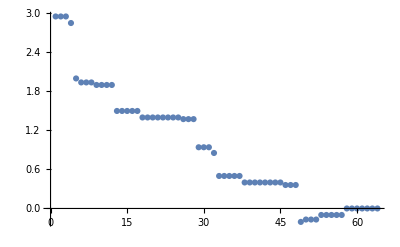

```mathematica
ListPlot[Eigenvalues[Hp]]
```

Eigenvectors

```mathematica
EVs =Eigenvectors[Hp];
```

Table of one-point functions

```mathematica
Tp = Table[tp[k, EVs], {k, 1, 2^M}];
```

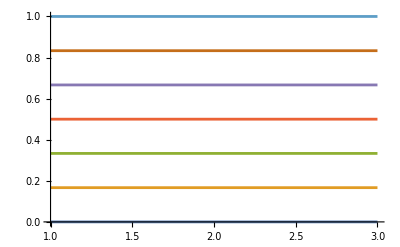

```mathematica
ListPlot[{Tp[[58]], Tp[[59]], Tp[[60]],Tp[[61]], Tp[[62]], Tp[[63]], Tp[[64]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

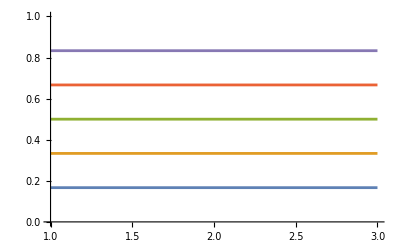

```mathematica
ListPlot[{Tp[[53]], Tp[[54]], Tp[[55]],Tp[[56]], Tp[[57]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

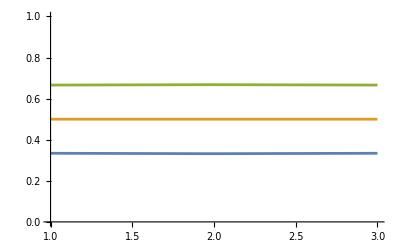

```mathematica
ListPlot[{Tp[[50]], Tp[[51]], Tp[[52]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

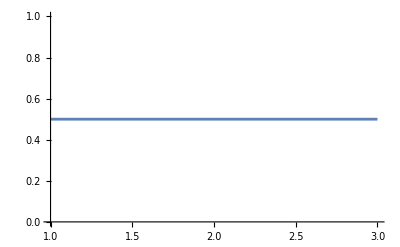

```mathematica
ListPlot[{Tp[[49]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

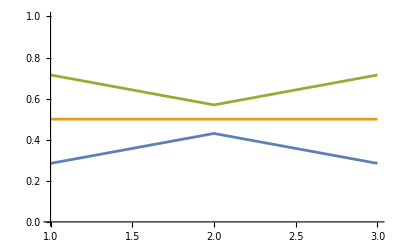

```mathematica
ListPlot[{Tp[[46]], Tp[[47]], Tp[[48]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

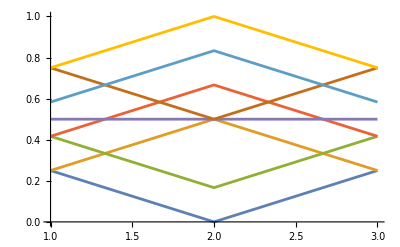

```mathematica
ListPlot[{Tp[[38]], Tp[[39]], Tp[[40]],Tp[[41]], Tp[[42]], Tp[[43]], Tp[[44]], Tp[[45]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

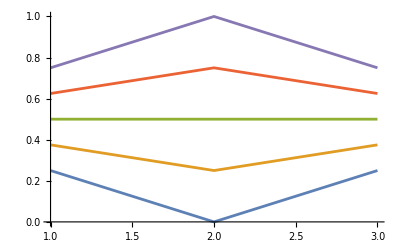

```mathematica
ListPlot[{Tp[[33]], Tp[[34]], Tp[[35]],Tp[[36]], Tp[[37]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

```mathematica
ListPlot[{Tp[[32]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

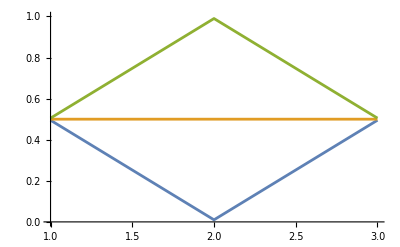

```mathematica
ListPlot[{Tp[[29]], Tp[[30]], Tp[[31]]}, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

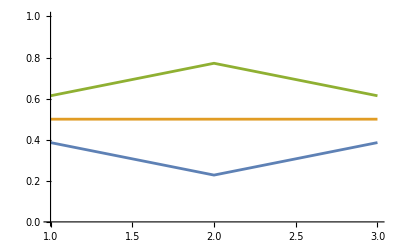

```mathematica
ListPlot[{Tp[[26]], Tp[[27]], Tp[[28]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

### Function for parallel rings

Here we write a function to produce the Hamiltonian for two parallel/stacked rings with a fixed number of down spins. 
CouplingStrength is the coefficient for the inter-ring Hamiltonian

```mathematica
TwoLayerHring[TotalSites_,SitesPerRing_,NumDownspins_,CouplingStrength_]:=Module[{HLayer1,HLayer2,H12,H,keepIndicesLayer1,keepIndicesLayer2},
{HLayer1, keepIndicesLayer1} = HringNdownspins[SitesPerRing,NumDownspins,Layer->True,LayerNum->1,M->TotalSites];
{HLayer2, keepIndicesLayer2} = HringNdownspins[SitesPerRing,NumDownspins,Layer->True,LayerNum->2,M->TotalSites];
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(SitesPerRing-1)], Sx, IdentityMatrix[2^(SitesPerRing-k)]], {k, 1, SitesPerRing}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(SitesPerRing-1)], Sy, IdentityMatrix[2^(SitesPerRing-k)]], {k, 1, SitesPerRing}]+ Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(SitesPerRing-1)], Sz, IdentityMatrix[2^(SitesPerRing-k)]], {k, 1, SitesPerRing}] - (SitesPerRing/4)IdentityMatrix[2^TotalSites];
H12 = H12[[keepIndicesLayer1,keepIndicesLayer1]];
H = -HLayer1 - HLayer2 +(CouplingStrength* H12);
{H,keepIndicesLayer1}
]
```

```mathematica
{H2Layer, IndicesKept} = TwoLayerHring[6,3,2,1/10];
MatrixForm[H2Layer]
```

(19/10 | -1 | -1
-1 | 19/10 | -1
-1 | -1 | 19/10)

### L=4

Let’s do two parallel lines

```mathematica
M=8;
L=4;
```

```mathematica
H1 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] ;
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}]+ Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M];
```

```mathematica
Hp = -H1 - H2 + (1/10)H12;
```

Eigenvalues

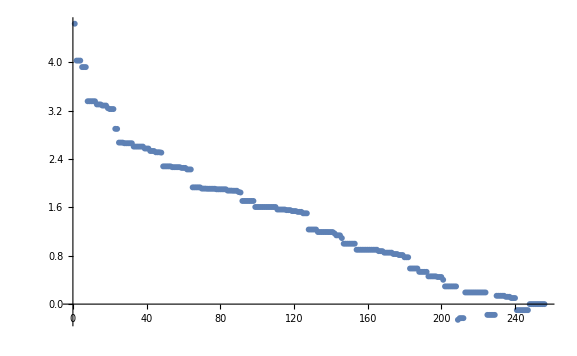

```mathematica
ListPlot[Eigenvalues[Hp]]
```

Eigenvectors

```mathematica
EVs =Eigenvectors[Hp];
```

Table of one-point functions.
WARNING: The code seems to break down. Not sure why. It seems like we are dividing by zero.

```mathematica
Tp = Table[tp[k, EVs], {k, 1, 2^M}];
```

General::munfl: 1.14204×10^-79 2.18165×10^-288 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.77277×10^-225 8.23469×10^-192 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.39508×10^-214 4.67109×10^-110 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Tp[[209]]
```

{{1,0.5},{2,0.5},{3,0.5},{4,0.5}}

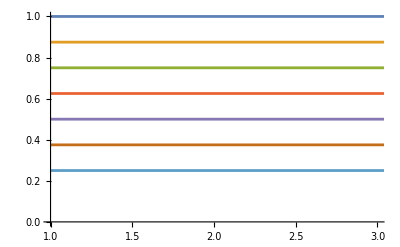

```mathematica
ListPlot[{Tp[[256]], Tp[[255]], Tp[[254]],Tp[[253]], Tp[[252]], Tp[[251]], Tp[[250]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

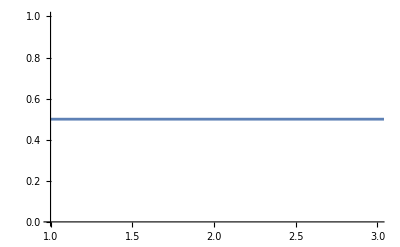

```mathematica
ListPlot[{Tp[[209]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

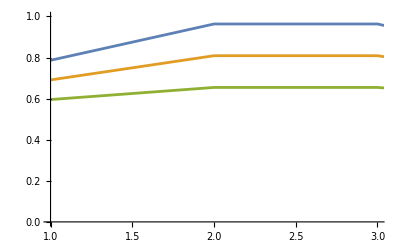

```mathematica
ListPlot[{Tp[[208]], Tp[[207]], Tp[[206]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

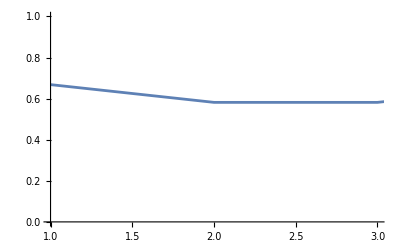

```mathematica
ListPlot[{Tp[[237]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

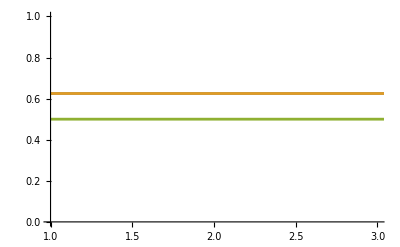

```mathematica
ListPlot[{Tp[[162]], Tp[[161]], Tp[[160]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

```mathematica
ListPlot[{Tp[[38]], Tp[[39]], Tp[[40]],Tp[[41]], Tp[[42]], Tp[[43]], Tp[[44]], Tp[[45]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[33]], Tp[[34]], Tp[[35]],Tp[[36]], Tp[[37]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[100]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[29]], Tp[[30]], Tp[[31]]}, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[26]], Tp[[27]], Tp[[28]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-